Incident points input and their plot

{{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}}

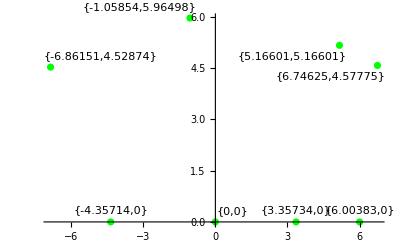

```mathematica
intersecpts = {{5.166010488516726,5.166010488516724},{6.003831069285709,0},{6.746248565974317,4.577754071440296},{3.357339206799729,0},{-1.058536173181429,5.964984411564576},{-4.357140119563605,0},{-6.861508969064321,4.528740458357809}, {0,0}}
intersecplot = ListPlot[Labeled[#,#] &/@ intersecpts, PlotRange->Full,PlotStyle->{Green}]
```

Separate the points into x -axis (plane mirror points) and unknown reflecting curve incident points

{{-6.86151,4.52874},{-1.05854,5.96498},{5.16601,5.16601},{6.74625,4.57775}}

{{-4.35714,0},{0,0},{3.35734,0},{6.00383,0}}

curvepts = {{-6.86151,4.52874},{-1.05854,5.96498},{5.16601,5.16601},{6.74625,4.57775}}

xaxispts = {{-4.35714,0},{0,0},{3.35734,0},{6.00383,0}}

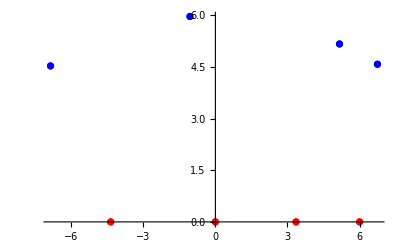

```mathematica
For[xaxispts = {}; i=0, i<Length[intersecpts], i++; If[intersecpts[[i, 2]]==0, AppendTo[xaxispts, intersecpts[[i]]]]]
curvepts = Sort[DeleteCases[intersecpts, Alternatives @@ xaxispts]]
xaxispts = Sort[xaxispts]
Print["curvepts = ", curvepts]
Print["xaxispts = ", xaxispts]
intersecplot2 = ListPlot[{#} & /@ intersecpts, PlotRange->Full,PlotStyle->{Blue, Red, Blue, Red, Blue, Red, Blue, Red}]
```

Equation for all permutations of lines for the 1st set of reflections

```mathematica
For[eqndataset = {}; z=0, z<Length[xaxispts], z++;
	For[pteqnmatrix = ConstantArray[0, {Length[curvepts]+1, Length[xaxispts]}]; i=0, i<Length[curvepts], i++;
		pteqnmatrix = ReplacePart[pteqnmatrix, 
		{1, i}->Last[List @@ Reduce[y-InterpolatingPolynomial[{xaxispts[[z]], curvepts[[i]]},x]==0,y]]];
		For[j=0, j<Length[xaxispts], j++; If[j==z, Continue[]];  
			pteqnmatrix = ReplacePart[pteqnmatrix, 
			{j+1, i}->{Last[List @@ Reduce[y - InterpolatingPolynomial[{curvepts[[i]], xaxispts[[j]]},x]==0,y]],
			Last[List @@ Reduce[y-0==-Coefficient[Last[List @@ Reduce[y - InterpolatingPolynomial[{curvepts[[i]], xaxispts[[j]]},x]==0,y]],x](x-xaxispts[[j]][[1]]),y]]}
		(* Reflection from the plane mirror added here simulatenously in set (left is incident, right is reflected *)
			]]];
	AppendTo[eqndataset, pteqnmatrix]]
eqndataset
eqndatasetcopy = eqndataset;
```

{{{-7.87917-1.80834 x,7.87917+1.80834 x,2.36361+0.542469 x,1.79638+0.412284 x},{0,0,0,0},{{0.-0.660021 x,0.+0.660021 x},{0.-5.63513 x,0.+5.63513 x},{0.+1. x,0.-1. x},{0.+0.678563 x,0.-0.678563 x}},{{1.48789-0.443175 x,-1.48789+0.443175 x},{4.53511-1.3508 x,-4.53511+1.3508 x},{-9.58939+2.85625 x,9.58939-2.85625 x},{-4.53511+1.3508 x,4.53511-1.3508 x}},{{2.11341-0.352011 x,-2.11341+0.352011 x},{5.07093-0.844615 x,-5.07093+0.844615 x},{37.0197-6.16601 x,-37.0197+6.16601 x},{-37.0197+6.16601 x,37.0197-6.16601 x}}},{{0.-0.660021 x,0.-5.63513 x,0.+1. x,0.+0.678563 x},{{-7.87917-1.80834 x,7.87917+1.80834 x},{7.87917+1.80834 x,-7.87917-1.80834 x},{2.36361+0.542469 x,-2.36361-0.542469 x},{1.79638+0.412284 x,-1.79638-0.412284 x}},{0,0,0,0},{{1.48789-0.443175 x,-1.48789+0.443175 x},{4.53511-1.3508 x,-4.53511+1.3508 x},{-9.58939+2.85625 x,9.58939-2.85625 x},{-4.53511+1.3508 x,4.53511-1.3508 x}},{{2.11341-0.352011 x,-2.11341+0.352011 x},{5.07093-0.844615 x,-5.07093+0.844615 x},{37.0197-6.16601 x,-37.0197+6.16601 x},{-37.0197+6.16601 x,37.0197-6.16601 x}}},{{1.48789-0.443175 x,4.53511-1.3508 x,-9.58939+2.85625 x,-4.53511+1.3508 x},{{-7.87917-1.80834 x,7.87917+1.80834 x},{7.87917+1.80834 x,-7.87917-1.80834 x},{2.36361+0.542469 x,-2.36361-0.542469 x},{1.79638+0.412284 x,-1.79638-0.412284 x}},{{0.-0.660021 x,0.+0.660021 x},{0.-5.63513 x,0.+5.63513 x},{0.+1. x,0.-1. x},{0.+0.678563 x,0.-0.678563 x}},{0,0,0,0},{{2.11341-0.352011 x,-2.11341+0.352011 x},{5.07093-0.844615 x,-5.07093+0.844615 x},{37.0197-6.16601 x,-37.0197+6.16601 x},{-37.0197+6.16601 x,37.0197-6.16601 x}}},{{2.11341-0.352011 x,5.07093-0.844615 x,37.0197-6.16601 x,-37.0197+6.16601 x},{{-7.87917-1.80834 x,7.87917+1.80834 x},{7.87917+1.80834 x,-7.87917-1.80834 x},{2.36361+0.542469 x,-2.36361-0.542469 x},{1.79638+0.412284 x,-1.79638-0.412284 x}},{{0.-0.660021 x,0.+0.660021 x},{0.-5.63513 x,0.+5.63513 x},{0.+1. x,0.-1. x},{0.+0.678563 x,0.-0.678563 x}},{{1.48789-0.443175 x,-1.48789+0.443175 x},{4.53511-1.3508 x,-4.53511+1.3508 x},{-9.58939+2.85625 x,9.58939-2.85625 x},{-4.53511+1.3508 x,4.53511-1.3508 x}},{0,0,0,0}}}

Plot of some reflections from source 1 to point 4

```mathematica
eqndataset[[1]] // MatrixForm
```

(-7.87917-1.80834 x | 7.87917+1.80834 x | 2.36361+0.542469 x | 1.79638+0.412284 x
0 | 0 | 0 | 0
{0.-0.660021 x,0.+0.660021 x} | {0.-5.63513 x,0.+5.63513 x} | {0.+1. x,0.-1. x} | {0.+0.678563 x,0.-0.678563 x}
{1.48789-0.443175 x,-1.48789+0.443175 x} | {4.53511-1.3508 x,-4.53511+1.3508 x} | {-9.58939+2.85625 x,9.58939-2.85625 x} | {-4.53511+1.3508 x,4.53511-1.3508 x}
{2.11341-0.352011 x,-2.11341+0.352011 x} | {5.07093-0.844615 x,-5.07093+0.844615 x} | {37.0197-6.16601 x,-37.0197+6.16601 x} | {-37.0197+6.16601 x,37.0197-6.16601 x})

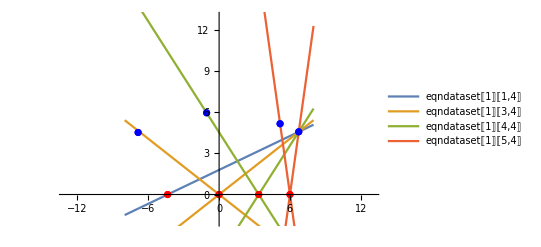

```mathematica
p1 = Plot[{eqndataset[[1]][[1,4]],eqndataset[[1]][[3,4]],eqndataset[[1]][[4,4]],eqndataset[[1]][[5,4]]}
, {x, -8, 8}, PlotLegends->"Expressions"];
Show[p1, intersecplot2, PlotRange->{{-13,13},{-2, 13}}]
```

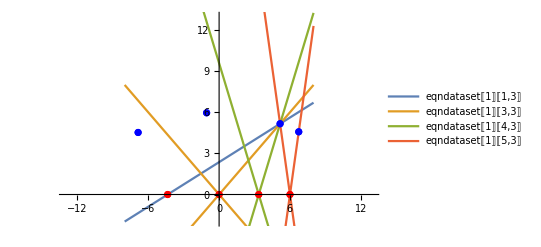

```mathematica
p1 = Plot[{eqndataset[[1]][[1,3]],eqndataset[[1]][[3,3]],eqndataset[[1]][[4,3]],eqndataset[[1]][[5,3]]}
, {x, -8, 8}, PlotLegends->"Expressions"];
Show[p1, intersecplot2, PlotRange->{{-13,13},{-2, 13}}]
```

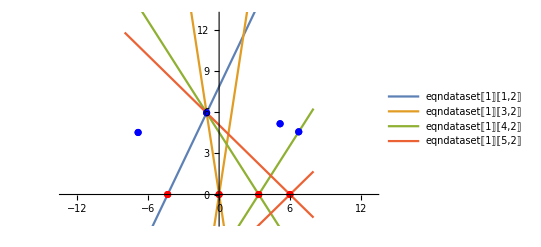

```mathematica
p1 = Plot[{eqndataset[[1]][[1,2]],eqndataset[[1]][[3,2]],eqndataset[[1]][[4,2]],eqndataset[[1]][[5,2]]}
, {x, -8, 8}, PlotLegends->"Expressions"];
Show[p1, intersecplot2, PlotRange->{{-13,13},{-2, 13}}]
```

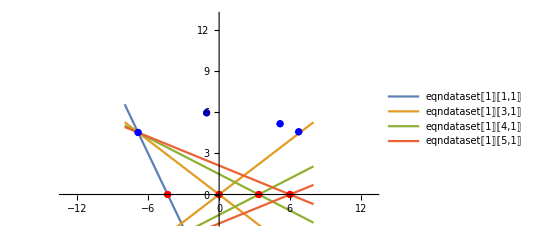

```mathematica
p1 = Plot[{eqndataset[[1]][[1,1]],eqndataset[[1]][[3,1]],eqndataset[[1]][[4,1]],eqndataset[[1]][[5,1]]}
, {x, -8, 8}, PlotLegends->"Expressions"];
Show[p1, intersecplot2, PlotRange->{{-13,13},{-2, 13}}]
```

Dropping the reflection equations which don’t satisfy the points. It can be done while making the matrix for optimization.

```mathematica
refleceqnlist = {};
For[p=0, p<Length[eqndataset], p++; 
	For[q=1, q<Length[eqndataset[[p]]], q++; 
		For[r=0, r<Length[eqndataset[[p]][[q]]], r++; If[eqndataset[[p]][[q,r]]==0, Continue[]]; eqn = y == eqndataset[[p]][[q,r]][[2]];
			For[s=0, s<Length[curvepts], s++; If[(eqn /. {x->curvepts[[s,1]], y->curvepts[[s,2]]})==True, 
				refleceqnlist = AppendTo[refleceqnlist, {eqn, curvepts[[s]]}]]]]]]
refleceqnlist
```

{{y==-4.53511+1.3508 x,{6.74625,4.57775}},{y==4.53511-1.3508 x,{-1.05854,5.96498}},{y==-37.0197+6.16601 x,{6.74625,4.57775}},{y==37.0197-6.16601 x,{5.16601,5.16601}},{y==7.87917+1.80834 x,{-1.05854,5.96498}},{y==-7.87917-1.80834 x,{-6.86151,4.52874}},{y==-4.53511+1.3508 x,{6.74625,4.57775}},{y==4.53511-1.3508 x,{-1.05854,5.96498}},{y==-37.0197+6.16601 x,{6.74625,4.57775}},{y==37.0197-6.16601 x,{5.16601,5.16601}},{y==7.87917+1.80834 x,{-1.05854,5.96498}},{y==-7.87917-1.80834 x,{-6.86151,4.52874}},{y==-37.0197+6.16601 x,{6.74625,4.57775}},{y==37.0197-6.16601 x,{5.16601,5.16601}},{y==7.87917+1.80834 x,{-1.05854,5.96498}},{y==-7.87917-1.80834 x,{-6.86151,4.52874}},{y==-4.53511+1.3508 x,{6.74625,4.57775}},{y==4.53511-1.3508 x,{-1.05854,5.96498}}}

Function for tuples of point combination

```mathematica
pttuplefunc[domainls_, codomainls_]:= 
	For[tupleset={};i=0, i<Length[domainls], i++;
		For[j=0, j<Length[codomainls], j++;
			tupleset = AppendTo[tupleset,{domainls[[i]], codomainls[[j]]}]]]
	tupleset
```

{{{-4.35714,0},{-6.86151,4.52874}},{{-4.35714,0},{-1.05854,5.96498}},{{-4.35714,0},{5.16601,5.16601}},{{-4.35714,0},{6.74625,4.57775}},{{0,0},{-6.86151,4.52874}},{{0,0},{-1.05854,5.96498}},{{0,0},{5.16601,5.16601}},{{0,0},{6.74625,4.57775}},{{3.35734,0},{-6.86151,4.52874}},{{3.35734,0},{-1.05854,5.96498}},{{3.35734,0},{5.16601,5.16601}},{{3.35734,0},{6.74625,4.57775}},{{6.00383,0},{-6.86151,4.52874}},{{6.00383,0},{-1.05854,5.96498}},{{6.00383,0},{5.16601,5.16601}},{{6.00383,0},{6.74625,4.57775}}}

Old Code with middle steps and plot

Line plots of the paths until no

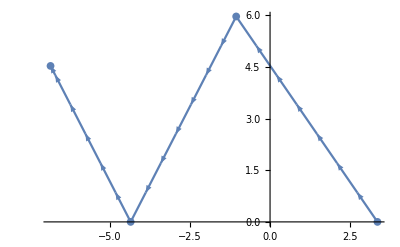

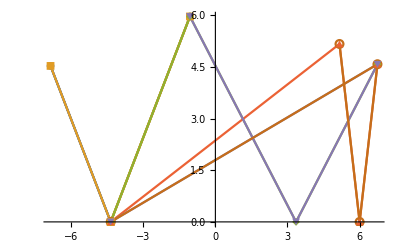

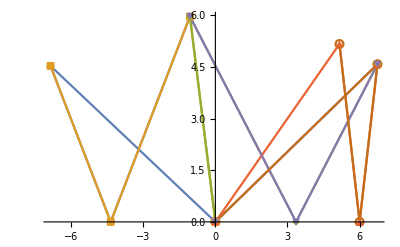

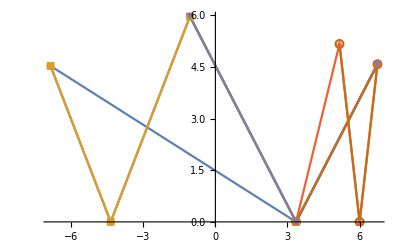

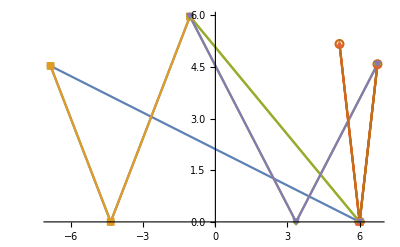

```mathematica
ListLinePlot[path1[[14]], PlotMarkers->{Automatic, 8}, Axes->True, AxesOrigin->{0,0}, MeshFunctions -> {#2 &}, Mesh -> 6, MeshStyle -> Opacity[0], 
  MeshShading -> {Arrowheads[Small]}, DataRange -> {0, 4 Pi}] /. Line -> Arrow
ListLinePlot[path1[[1;;6]], PlotMarkers->{Automatic, 8}, Axes->True, AxesOrigin->{0,0}]
ListLinePlot[path1[[7;;12]], PlotMarkers->{Automatic, 8}, Axes->True, AxesOrigin->{0,0}]
ListLinePlot[path1[[13;;18]], PlotMarkers->{Automatic, 8}, Axes->True, AxesOrigin->{0,0}]
ListLinePlot[path1[[19;;24]], PlotMarkers->{Automatic, 8}, Axes->True, AxesOrigin->{0,0}]
```

```mathematica
path2func[path_]:= 
	Module[{temp2={}},
		For[i=0, i<Length[path], i++;
			For[j=0, j<Length[xaxispts], j++;
				temp2 = Append[temp2, Join[path[[i]], {xaxispts[[j]]}]]]; Print[temp2]];
		temp2]
```

```mathematica
path2 = path2func[path1];
```

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}}}

64

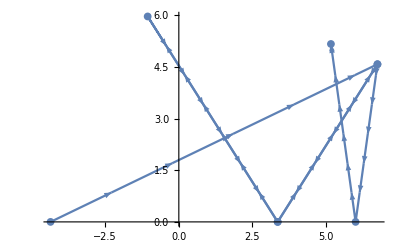

```mathematica
path3 = reflecdrop[path2]//Quiet
a = reflecdrop[path2func[path3]]//Quiet
Length[a]
```

```mathematica
ListLinePlot[a[[25]], PlotMarkers->{Automatic, 8}, Axes->True, AxesOrigin->{0,0}, MeshFunctions -> {#2 &}, Mesh -> 6, MeshStyle -> Opacity[0], 
  MeshShading -> {Arrowheads[Small]}, DataRange -> {0, 4 Pi}] /. Line -> Arrow

For[new={}; i=0, i<Length[a], i++;
	If[CountDistinct[a[[i]]]==Length[intersecpts], new = AppendTo[new, a[[i]]]]]
new
```

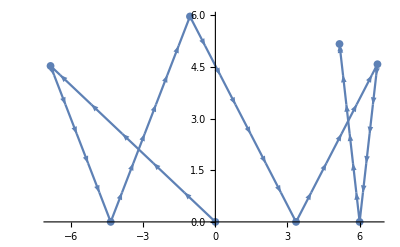

```mathematica
ListLinePlot[new[[1]], PlotMarkers->{Automatic, 8}, Axes->True, AxesOrigin->{0,0}, MeshFunctions -> {#2 &}, Mesh -> 6, MeshStyle -> Opacity[0], 
  MeshShading -> {Arrowheads[Small]}, DataRange -> {0, 4 Pi}] /. Line -> Arrow
```